## Draft Computational Essay

#### Introduction

Multiway systems are systems generated by a set of rules that are recursively applied to all of the outputs.

#### Observations

Generally, with a linear or multiplicative multiway systems, merging behavior can be predicted by the various constant values.

Consider a system of the form

```mathematica
n |-> {an, n + b}
```

With this, we can predict the initial grid like pattern that arises, at least from the lower level branches.

```mathematica
Graph[With[{g=ResourceFunction["NestGraphTagged"][x|->Expand[{5x,x+3}],{n},6,"StateLabeling"->True]},Subgraph[g,First/@First[FindCycle[UndirectedGraph[g],{8}]]]]]
```

-Graphics-

where the left hand side will always have a+1 sides, and the right hand side has 2 sides, resulting in (a+3)-gons, as explained by Stephen Wolfram’s work “Multicomputation with Numbers: The Case of Simple Multiway Systems”. However, there are some exceptions to this behavior.  
For example, consider the rule set

```mathematica
n|->{2n, n+5}
```

The resulting graph ends up with one heptagon, with the remaining grids being pentagons. Every pentagon is also in the format of the generalized (n+3)-gon as explained above, which is trivial to see.

```mathematica
ResourceFunction["NestGraphTagged"][n↦{2n, n+5},{1},7,"StateLabeling"->True, PlotLegends->TraditionalForm/@{2n, n+5}]
```

-Graphics-

Zooming in on the heptagon subset, we see

```mathematica
Graph[With[{g=ResourceFunction["NestGraphTagged"][x|->Expand[{2x,x+5}],{1},6,"StateLabeling"->True]},Subgraph[g,First/@First[FindCycle[UndirectedGraph[g],{7}]]]]]
```

-Graphics-

Conveniently,

```mathematica
∃x∈Ζ^+ | a^x
```

and this can easily be seen as true, as an integer x would exist through Fermat’s Little Theorem, since a and b are relatively prime.

#### Dyck Paths

Dyck paths are lattice paths from (0, 0) to (n, n)that do not pass above the diagonal (y=x). For example, here’s an Dyck path where n=6.

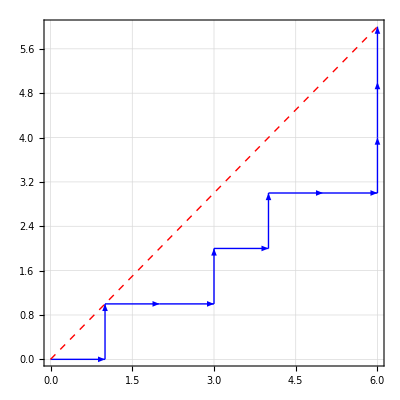

From any given point, a path can be generated by the map

```mathematica
{x, y} |-> {{x+1, y}, {x,y+1}}
```

or simply right and up “moves”. However, to make this path into a Dyck path, we will have to consider the restriction of the diagonal.

I opted to store the Dyck path by a list of the heights of the columns. For the example Dyck path above, it would be stored as

```mathematica
{0, 1, 1, 2, 3, 3, 6}
```

The 6 at the end is technically not in the graph itself, but makes the conversion graphically, which will be explained later, much less convoluted.

To turn this into a multiway graph, I recursively build the next step of